# O^16/O^18 kinetic isotope effect for ET reaction in superoxide dismutase

Alexander V. Soudackov
Pennsylvania State University, University Park, PA 16802.

## Unit conversion factors, constants, etc.

```mathematica
bohr2a=0.529177;
```

```mathematica
au2kcal=627.5095;
```

```mathematica
ev2cm=8065.54477;
cm2ev = 1/ev2cm ;
au2ev=27.2113 ;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
```

```mathematica
ℏ=1;
ℏps=0.047685388/(π au2kcal);
```

Boltzmann constant (a.u./K)

```mathematica
kb=0.0019872159/au2kcal;
```

AMU in electron mass units

```mathematica
Dalton=1822.8880;
```

```mathematica
β[T_]:=1/(kb T);
```

## System parameters

Driving force (a.u.):

```mathematica
ΔG = 10.38/au2kcal;
```

Reorganization energy (a.u.):

```mathematica
λ=28.43/au2kcal;
```

Electronic coupling (a.u.):

```mathematica
V=0.01/au2kcal;
```

Frequencies for dioxygen and superoxide (with "s")(a.u.):

```mathematica
ω16=1556 cm2au;
ω16s=1065 cm2au;
ω18=1512 cm2au;
ω18s=1035 cm2au;
```

Average O-O frequencies

```mathematica
Ω16=(2ω16 ω16s)/(ω16+ω16s);
Ω18=(2ω18 ω18s)/(ω18+ω18s);
```

Reduced masses (electron mass):

```mathematica
μ16=7.9975 Dalton;
μ18=8.4690 Dalton;
```

Equilibrium O-O distances (Bohr):

```mathematica
ROO=1.208/bohr2a;
ROOs1=1.308/bohr2a;
ROOs2=1.328/bohr2a;
d1=ROOs1-ROO;
d2=ROOs2-ROO;
```

Morse parameters:

```mathematica
DOO=85/au2kcal;
DOOs=85/au2kcal;
```

β (A^-1)is calculated from the frequency ω (a.u.),dissociation energy (a.u.) and
mass

```mathematica
β16=ω16 √(μ16/(2DOO));
β16s=ω16s √(μ16/(2DOOs));
β18=ω18 √(μ18/(2DOO));
β18s=ω18s √(μ18/(2DOOs));
```

β's for average frequencies:

```mathematica
βa16=Ω16 √(μ16/(DOO+DOOs));
βa18=Ω18 √(μ18/(DOO+DOOs));
```

## Harmonic oscillator wavefunctions and overlaps

Wavefunctions (atomic units):

```mathematica
ψ[x_,x0_,n_,ω_,μ_]:=((μ ω)/(π ℏ))^(1/4)1/(2^(n/2)√(n!))Exp[-(μ ω)/(2ℏ) (x-x0)^2]HermiteH[n,(x-x0)√((μ ω)/ℏ)];
```

Energies (atomic units):

```mathematica
ϵ[n_,ω_]:=ℏ ω(n+1/2);
```

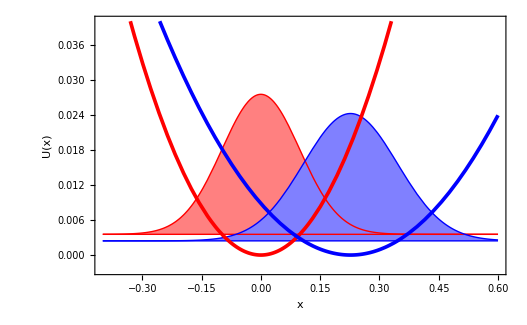

```mathematica
Plot[Tooltip[{ϵ[0,ω16],0.01ψ[x,0,0,ω16,μ16]+ϵ[0,ω16],ϵ[0,ω16s],0.01ψ[x,d2,0,ω16s,μ16]+ϵ[0,ω16s],1/2 μ16 ω16^2 x^2,1/2 μ16 ω16s^2(x-d2)^2}],{x,-0.4,0.6},Frame->True,Axes->False,PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[0,0,1],RGBColor[0,0,1],{RGBColor[1,0,0],Thickness[0.005]},{RGBColor[0,0,1],Thickness[0.005]}},Filling->{1->{{2},RGBColor[1,0.5,0.5]},3->{{4},RGBColor[0.5,0.5,1]}},PlotRange->{-0.0025,0.04},FillingStyle->Directive[Opacity[0.5]],FrameLabel->{{U[x],Subscript[ψ, 0][x]},{x,"Overlap of two ground state wavefunctions for shifted oscillators"}}]
```

#### Overlap integrals S_nm=∫_(-∞)^∞ ψ_n(x)ψ_m(x+Δ)ⅆx (analytical expression due to J.-L. Chang [J.-L. Chang, J. Mol. Spectrosc. 232 (2005) 102-104]:

Auxiliary function:

```mathematica
K[i_,j_,a_,b_]:=If[OddQ[i+j],0,((i+j-1)!!)/(a+b)^((i+j)/2)];
```

Overlap integral <ψ_n|ψ_m> (ω1, ω2 - corresponding frequencies; μ - reduced mass; d - displacement):

```mathematica
S=Function[{n,m,ω1,ω2,μ,d},
α1=(μ ω1)/ℏ;
α2=(μ ω2)/ℏ;
s=(α1 α2 d^2)/(α1+α2);
A=(2 √(α1 α2))/(α1+α2);
Prefactor=√((A Exp[-s])/(2^(n+m)n!m!));
b1=-(d α2 √α1)/(α1+α2);
b2=(d α1 √α2)/(α1+α2);
Prefactor∑_(i=0)^n (∑_(j=0)^m (Binomial[n,i]Binomial[m,j]HermiteH[n-i,b1]HermiteH[m-j,b2](2 √α1)^i(2 √α2)^j K[i,j,α1,α2]))

];
```

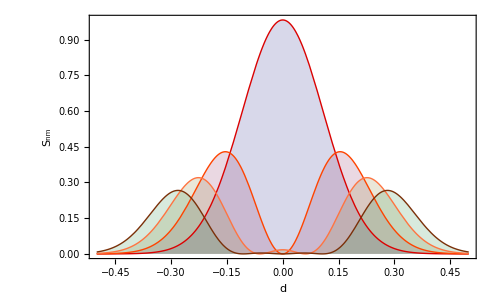

```mathematica
Plot[Evaluate[Table[S[0,f,ω16,ω16s,μ16,x]^2,{f,0,3}]],{x,-0.5,0.5},Frame->True,Axes->False,FrameLabel->{d,"S_nm","Squared Overlap integral vs. displacement"},Filling->Axis,PlotStyle->ColorData[2,"ColorList"]]
```

## Morse oscillator wavefunctions and overlaps

Potentials (centered at zero):

```mathematica
U16[x_]:=DOO(1-Exp[-β16 x])^2;
U16s[x_]:=DOOs(1-Exp[-β16s x])^2;
U18[x_]:=DOO(1-Exp[-β18 x])^2;
U18s[x_]:=DOOs(1-Exp[-β18s x])^2;
```

```mathematica
λ16=(√(2μ16 DOO))/(β16 ℏ);
λ16s=(√(2μ16 DOOs))/(β16s ℏ);
λ18=(√(2μ18 DOO))/(β18 ℏ);
λ18s=(√(2μ18 DOOs))/(β18s ℏ);
```

```mathematica
ξ16[x_]:=2λ16 Exp[-β16 x];
ξ16s[x_]:=2λ16s Exp[-β16s x];
ξ18[x_]:=2λ18 Exp[-β18 x];
ξ18s[x_]:=2λ18s Exp[-β18s x];
```

Energy levels:

```mathematica
E16[n_]:=((n+1/2)-1/(2λ16)(n+1/2)^2)ℏ √((2DOO β16^2)/μ16);
E16s[n_]:=((n+1/2)-1/(2λ16s)(n+1/2)^2)ℏ √((2DOOs β16s^2)/μ16);
E18[n_]:=((n+1/2)-1/(2λ18)(n+1/2)^2)ℏ √((2DOO β18^2)/μ18);
E18s[n_]:=((n+1/2)-1/(2λ18s)(n+1/2)^2)ℏ √((2DOOs β18s^2)/μ18);
```

Normalization constants (for wavefunctions):

```mathematica
N16[n_]:=√((β16(2λ16-2n-1)Gamma[n+1])/Gamma[2λ16-n]);
N16s[n_]:=√((β16s(2λ16s-2n-1)Gamma[n+1])/Gamma[2λ16s-n]);
```

```mathematica
N18[n_]:=√((β18(2λ18-2n-1)Gamma[n+1])/Gamma[2λ18-n]);
N18s[n_]:=√((β18s(2λ18s-2n-1)Gamma[n+1])/Gamma[2λ18s-n]);
```

Normalized Morse Wavefunctions:

```mathematica
ϕ16[x_,n_]:=N16[n]Exp[-ξ16[x]/2] ξ16[x]^(λ16-n-1/2)LaguerreL[n,2λ16-2n-1,ξ16[x]];ϕ18[x_,n_]:=N18[n]Exp[-ξ18[x]/2] ξ18[x]^(λ18-n-1/2)LaguerreL[n,2λ18-2n-1,ξ18[x]];
ϕ16s[x_,n_]:=N16s[n]Exp[-ξ16s[x]/2] ξ16s[x]^(λ16s-n-1/2)LaguerreL[n,2λ16s-2n-1,ξ16s[x]];ϕ18s[x_,n_]:=N18s[n]Exp[-ξ18s[x]/2] ξ18s[x]^(λ18s-n-1/2)LaguerreL[n,2λ18s-2n-1,ξ18s[x]];
```

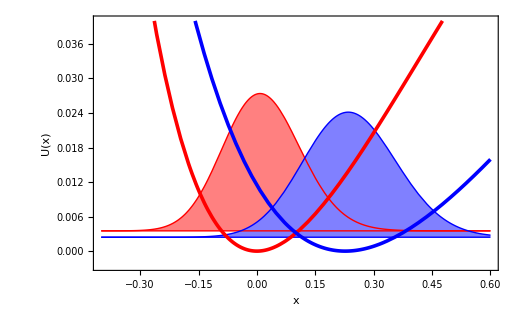

```mathematica
Plot[Tooltip[{E16[0],0.01ϕ16[x,0]+E16[0],E16s[0],0.01ϕ16s[x-d2,0]+E16s[0],U16[x],U16s[x-d2]}],{x,-0.4,0.6},Frame->True,Axes->False,PlotStyle->{RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[0,0,1],RGBColor[0,0,1],{RGBColor[1,0,0],Thickness[0.005]},{RGBColor[0,0,1],Thickness[0.005]}},Filling->{1->{{2},RGBColor[1,0.5,0.5]},3->{{4},RGBColor[0.5,0.5,1]}},PlotRange->{-0.0025,0.04},FillingStyle->Directive[Opacity[0.5]],FrameLabel->{{U[x],Subscript[ϕ, 0][x]},{x,"Overlap of two ground state wavefunctions for shifted Morse oscillators"}}]
```

Overlap integrals (numerical):

```mathematica
S16=Function[{δ,n,m},NIntegrate[ϕ16[x,n]ϕ16s[x+δ,m],{x,-∞,∞}]];
S18=Function[{δ,n,m},NIntegrate[ϕ18[x,n]ϕ18s[x+δ,m],{x,-∞,∞}]];
```

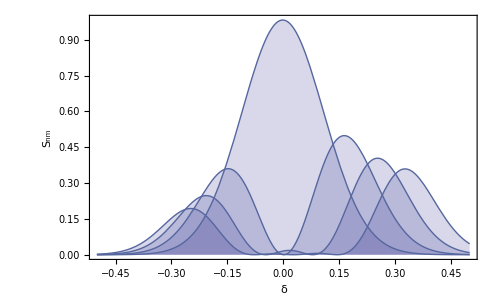

```mathematica
Plot[Table[S16[x,0,f]^2,{f,0,3}],{x,-0.5,0.5},Frame->True,Axes->False,PlotRange->All,FrameLabel->{δ,"S_nm","Squared Overlap integral (Morse) vs. displacement"},Filling->Axis,PlotStyle->ColorData[2,"ColorList"]]
```

## Rate expression

The rate expression is obtained in the first order perturbation theory (Golden Rule) for transitions between the sets of reactant and product vibronic states, defined as
Ψ_Rμ(r_e,Q)=Φ_R(r_e|Q_R)χ_Rμ(Q-Q_R)
Ψ_Pν(r_e,Q)=Φ_P(r_e|Q_P)χ_Pν(Q-Q_P)
where χ_Rμ(Q), χ_Pν(Q) are the harmonic vibrational wavefunctions; Q_R, Q_P are the equilibrium positions of the reactant and product oscillators. The rate is given as Boltzmann weighted average of the transition probabilities from the reactant vibronic states to all product vibronic states:
k=(2π)/ℏ V^2∑_μ P_μ∑_ν (S_μν^2(4πλ k T))^(1/2)exp[-(ΔG+λ+Δϵ_μν)^2/(4λ k T)]
where the electronic coupling V=<Φ_R|H|Φ_P>, reaction free energy ΔG, reorganization energy λ are assumed to be the same for all pairs of vibrational states.

Vibrational partition function (zero energy is at the bottom of the reactant potential well):

```mathematica
Z[ω_,T_]:=1/(Exp[(β[T]ℏ ω)/2]-Exp[-(β[T]ℏ ω)/2]);
```

```mathematica
ZP[ω_,T_,Δ_]:=Exp[-β[T]Δ] 1/(Exp[(β[T]ℏ ω)/2]-Exp[-(β[T]ℏ ω)/2]);
```

Boltzmann weights:

```mathematica
P[n_,ω_,T_]:=1/Z[ω,T] Exp[-β[T](n+1/2)ℏ ω];
```

Rate expression:

Partial rate of transition ii→jj.
Arguments (all in atomic units, unless specified):
Δ - reaction free energy (energy bias);
T - temperature (K);
μ - reduced mass;
ii - initial state quantum number (starts with 0 for reactant ground state);
jj - final state quantum number  (starts with 0 for product ground state);
ω1, ω2 - reactant and product frequencies, respectively;
d - displacement, defined as d=R_OO(product) - R_OO(reactant).
(M16 and M18 are for Morse oscillators)

```mathematica
kpartial[Δ_,T_,μ_,ii_,jj_,ω1_,ω2_,d_]:=10^12(2π)/ℏps V^2((4π λ)/β[T])^(-1/2)S[ii,jj,ω1,ω2,μ,d]^2 Exp[-β[T](Δ+λ+ϵ[jj,ω2]-ϵ[ii,ω1])^2/(4λ)];
kpartialM16[Δ_,T_,ii_,jj_,d_]:=10^12(2π)/ℏps V^2((4π λ)/β[T])^(-1/2)S16[d,ii,jj]^2 Exp[-β[T](Δ+λ+E16s[jj]-E16[ii])^2/(4λ)];
kpartialM18[Δ_,T_,ii_,jj_,d_]:=10^12(2π)/ℏps V^2((4π λ)/β[T])^(-1/2)S18[d,ii,jj]^2 Exp[-β[T](Δ+λ+E18s[jj]-E18[ii])^2/(4λ)];
```

Total rate (including transitions from nn lowest reactant states to mm lowest product states):

```mathematica
k[Δ_,T_,μ_,nn_,mm_,ω1_,ω2_,d_]:=∑_(ii=0)^nn (P[ii,ω1,T]∑_(jj=0)^mm (kpartial[Δ,T,μ,ii,jj,ω1,ω2,d]));
kM16[Δ_,T_,nn_,mm_,d_]:=∑_(ii=0)^nn (P[ii,ω16,T]∑_(jj=0)^mm (kpartialM16[Δ,T,ii,jj,d]));
kM18[Δ_,T_,nn_,mm_,d_]:=∑_(ii=0)^nn (P[ii,ω18,T]∑_(jj=0)^mm (kpartialM18[Δ,T,ii,jj,d]));
```

```mathematica
ratecontributions=Function[{Δ,T,μ,n,m,ω1,ω2,d},
totalrate=k[Δ,T,μ,n,m,ω1,ω2,d];TableForm[Table[EngineeringForm[(P[i,ω1,T]kpartial[Δ,T,μ,i,j,ω1,ω2,d])/totalrate 100,3,ExponentStep->2],{i,0,n},{j,0,m}],TableHeadings->{Table[kr,{kr,0,n}],Table[kp,{kp,0,m}]}]];
ratecontributionsM16=Function[{Δ,T,n,m,d},
totalrateM16=kM16[Δ,T,n,m,d];TableForm[Table[EngineeringForm[(P[i,ω16,T]kpartialM16[Δ,T,i,j,d])/totalrateM16 100,3,ExponentStep->2],{i,0,n},{j,0,m}],TableHeadings->{Table[kr,{kr,0,n}],Table[kp,{kp,0,m}]}]];
ratecontributionsM18=Function[{Δ,T,n,m,d},
totalrateM18=kM18[Δ,T,n,m,d];TableForm[Table[EngineeringForm[(P[i,ω18,T]kpartialM18[Δ,T,i,j,d])/totalrateM18 100,3,ExponentStep->2],{i,0,n},{j,0,m}],TableHeadings->{Table[kr,{kr,0,n}],Table[kp,{kp,0,m}]}]];
```

Contributions of different channels (i→j) (%):

```mathematica
ratecontributions[ΔG,300,μ16,5,5,ω16,ω16s,d1]
```

| 0 | 1 | 2 | 3 | 4 | 5
0 | 88.3 | 4.47 | 6.9×10^-2 | 3.94×10^-4 | 75.8×10^-8 | 2.07×10^-10
1 | 6.86 | 5.75×10^-2 | 28.7×10^-4 | 2.65×10^-4 | 3.65×10^-6 | 1.37×10^-8
2 | 19.8×10^-2 | 5.42×10^-4 | 3.99×10^-4 | 23.4×10^-8 | 48.6×10^-8 | 1.82×10^-8
3 | 25.6×10^-4 | 1.44×10^-4 | 5.27×10^-6 | 44.1×10^-8 | 1.68×10^-8 | 3.93×10^-10
4 | 16.×10^-6 | 3.66×10^-6 | 20.1×10^-10 | 2.36×10^-8 | 36.8×10^-12 | 63.2×10^-12
5 | 5.07×10^-8 | 3.19×10^-8 | 16.9×10^-10 | 1.56×10^-10 | 30.3×10^-12 | 58.3×10^-14

For Morse oscillators:

```mathematica
ratecontributionsM16[ΔG,300,2,2,d1]
```

| 0 | 1 | 2
0 | 89.4 | 5.84 | 8.36×10^-2
1 | 4.48 | 3.65×10^-2 | 72.8×10^-4
2 | 10.6×10^-2 | 8.07×10^-6 | 2.32×10^-4

Convergence of the rate constant with the number of reactant and product states:

```mathematica
ListPlot3D[Table[10^10 k[ΔG,300,μ16,i,j,ω16,ω16s,d1],{i,0,7},{j,0,7}],AxesLabel->{m[product],n [reactant]}]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[10^10 kM16[ΔG,300,i,j,d1],{i,0,5},{j,0,5}],AxesLabel->{m[product],n [reactant]}]
```

-Graphics3D-

## Kinetic Isotope Effect (KIE)

```mathematica
KIE[Δ_,T_,μ1_,μ2_,n_,m_,ω1_,ω1s_,ω2_,ω2s_,d_]:=k[Δ,T,μ1,n,m,ω1,ω1s,d]/k[Δ,T,μ2,n,m,ω2,ω2s,d];
KIEM[Δ_,T_,n_,m_,d_]:=kM16[Δ,T,n,m,d]/kM18[Δ,T,n,m,d];
```

## Calculations

```mathematica
k[ΔG,300,μ16,0,0,ω16,ω16s,d1]
```

0.30945

```mathematica
kM16[ΔG,300,0,0,d1]
```

0.309297

Equilibrium constant:

```mathematica
Exp[-β[300]ΔG]
```

2.74392×10^-8

Ratio of reactant and product partition functions:

```mathematica
ZP[ω16s,300,ΔG]/Z[ω16,300]
```

8.95558×10^-8

Ratio of forward and backward rate constants shoud be equal to the inverse ratio of partition functions:

k_forward/k_backward=Z_product/Z_reactant

Let's check if it holds in our case:

```mathematica
k[ΔG,300,μ16,0,0,ω16,ω16s,d1]/k[-ΔG,300,μ16,0,0,ω16s,ω16,d1]
```

8.95558×10^-8

```mathematica
k[ΔG,300,μ16,5,5,ω16,ω16s,d1]/k[-ΔG,300,μ16,5,5,ω16s,ω16,d1]
```

8.95558×10^-8

For average frequencies:

```mathematica
ZP[Ω16,300,ΔG]/Z[Ω16,300]
```

2.74392×10^-8

```mathematica
k[ΔG,300,μ16,5,5,Ω16,Ω16,d1]/k[-ΔG,300,μ16,5,5,Ω16,Ω16,d1]
```

2.74392×10^-8

Isotope Effects:

```mathematica
KIE[ΔG,300,μ16,μ18,5,5,ω16,ω16s,ω18,ω18s,d1]
```

1.05181

```mathematica
KIE[ΔG,300,μ16,μ18,5,5,Ω16,Ω16,Ω18,Ω18,d1]
```

1.0247

```mathematica
KIEM[ΔG,300,5,5,d1]
```

1.05197

```mathematica
KIE[ΔG,300,μ16,μ18,5,5,ω16,ω16s,ω18,ω18s,d2]
```

1.06501

```mathematica
KIE[ΔG,300,μ16,μ18,5,5,Ω16,Ω16,Ω18,Ω18,d2]
```

1.03601

```mathematica
KIEM[ΔG,300,5,5,d2]
```

1.06512

Ratio of KIE's for forward and backward reactions:

```mathematica
KIE[ΔG,300,μ16,μ18,5,5,ω16,ω16s,ω18,ω18s,d1]/KIE[-ΔG,300,μ16,μ18,5,5,ω16s,ω16,ω18s,ω18,d1]
```

1.03331

The same ratio for average frequencies:

```mathematica
KIE[ΔG,300,μ16,μ18,5,5,Ω16,Ω16,Ω18,Ω18,d1]/KIE[-ΔG,300,μ16,μ18,5,5,Ω16,Ω16,Ω18,Ω18,d1]
```

1.

KIE temperature dependence (Log(KIE) vs. 1/T):

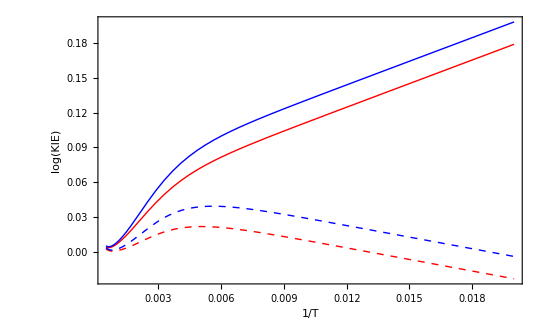

```mathematica
Plot[{Log[KIE[ΔG,1/x,μ16,μ18,5,5,ω16,ω16s,ω18,ω18s,d1]],Log[KIE[ΔG,1/x,μ16,μ18,5,5,ω16,ω16s,ω18,ω18s,d2]],Log[KIE[-ΔG,1/x,μ16,μ18,5,5,ω16s,ω16,ω18s,ω18,d1]],Log[KIE[-ΔG,1/x,μ16,μ18,5,5,ω16s,ω16,ω18s,ω18,d2]]},{x,1/2000,1/50},Frame->True,Axes->True,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},FrameLabel->{1/T,Log[KIE]}]
```

For Morse oscillators (forward reaction):

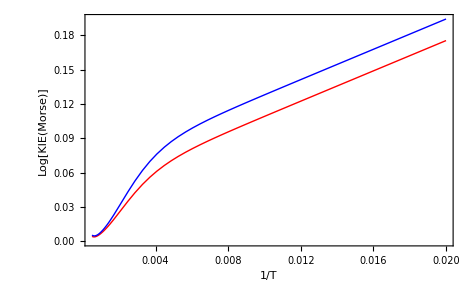

```mathematica
Plot[{Log[KIEM[ΔG,1/x,5,5,d1]],Log[KIEM[ΔG,1/x,5,5,d2]]},{x,1/2000,1/50},Frame->True,Axes->True,PlotStyle->{Red,Blue},FrameLabel->{"1/T","Log[KIE(Morse)]"}]
```

Dependence of the rate on the reaction free energy (at T=300K, dashed lines are for the reverse reaction) (Marcus plots):

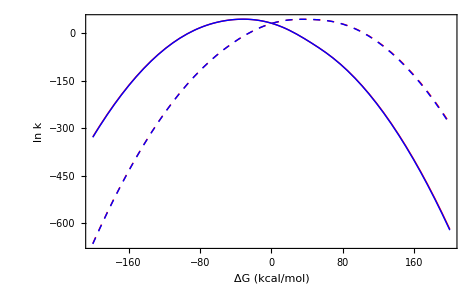

```mathematica
Plot[{Log[10^10 k[Δ/au2kcal,300,μ16,5,5,ω16,ω16s,d1]],Log[10^10 k[Δ/au2kcal,300,μ18,5,5,ω18,ω18s,d1]],Log[10^10 k[-Δ/au2kcal,300,μ16,5,5,ω16s,ω16,d1]],Log[10^10 k[-Δ/au2kcal,300,μ18,5,5,ω18s,ω18,d1]]},{Δ,-200,200},Frame->True,Axes->True,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},FrameLabel->{"ΔG (kcal/mol)","ln k"}]
```

Dependence of the KIE on the reaction free energy (at T=300K, dashed lines are for the reverse reaction):

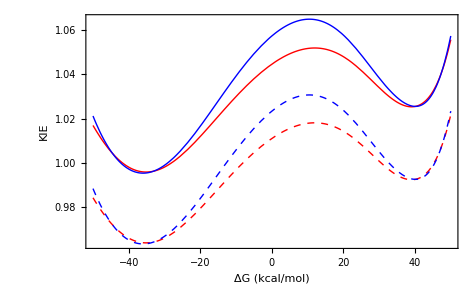

```mathematica
Plot[{KIE[Δ/au2kcal,300,μ16,μ18,5,5,ω16,ω16s,ω18,ω18s,d1],KIE[Δ/au2kcal,300,μ16,μ18,5,5,ω16,ω16s,ω18,ω18s,d2],KIE[-Δ/au2kcal,300,μ16,μ18,5,5,ω16s,ω16,ω18s,ω18,d1],KIE[-Δ/au2kcal,300,μ16,μ18,5,5,ω16s,ω16,ω18s,ω18,d2]},{Δ,-50,50},Frame->True,Axes->False,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},FrameLabel->{"ΔG (kcal/mol)",KIE}]
```

Dependence of the KIE on the reaction free energy for average frequencies (at T=300K, dashed lines are for the reverse reaction):

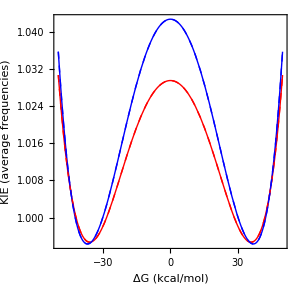

```mathematica
Plot[{KIE[Δ/au2kcal,300,μ16,μ18,5,5,Ω16,Ω16,Ω18,Ω18,d1],KIE[Δ/au2kcal,300,μ16,μ18,5,5,Ω16,Ω16,Ω18,Ω18,d2],KIE[-Δ/au2kcal,300,μ16,μ18,5,5,Ω16,Ω16,Ω18,Ω18,d1],KIE[-Δ/au2kcal,300,μ16,μ18,5,5,Ω16,Ω16,Ω18,Ω18,d2]},{Δ,-50,50},Frame->True,Axes->False,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}},FrameLabel->{"ΔG (kcal/mol)","KIE (average frequencies)"}]
```

The same for the Morse oscillators (forward rates):

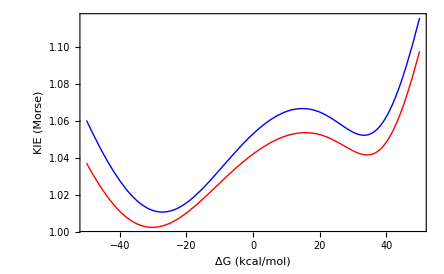

```mathematica
Plot[{KIEM[Δ/au2kcal,300,2,2,d1],KIEM[Δ/au2kcal,300,2,2,d2]},{Δ,-50,50},Frame->True,Axes->False,PlotStyle->{Red,Blue},FrameLabel->{"ΔG (kcal/mol)","KIE (Morse)"}]
```